## Load Data

```mathematica
(*Non timed response data. When Importing change to right directory. Amount of bet couples =80, n= 41 *)
Choice=Flatten[Round[Import["C:\\Users\\arnev\\Documents\\Wolfram Mathematica\\Matrix_Not_Timed.xlsx"],1],1];
```

```mathematica
(*Timed response data. When Importing change to right directory. Amount of bet couples =80, n= 40 *)
Choice=Flatten[Round[Import["C:\\Users\\arnev\\Documents\\Wolfram Mathematica\\Matrix_Timed.xlsx"],1],1];
```

```mathematica
(*All Response Data. When Importing change to right directory. Amount of bet couples =80, n= 41. safe bet chosen = 1, risky bet chosen = 0  *)
Choice=Flatten[Round[Import["C:\\Users\\arnev\\Documents\\Wolfram Mathematica\\Cleanest_Matrix.xlsx"],1],1];
```

```mathematica
(*Bet Couples*)betCouples={{{{1/2,-308},{1/2,291}},{{1/2,-88},{1/2,71}}},{{{1/2,-543},{1/2,554}},{{1/2,100},{1/2,-89}}},{{{1/2,692},{1/2,-523}},{{1/2,-254},{1/2,423}}},{{{1/2,683},{1/2,-670}},{{1/2,-114},{1/2,127}}},{{{1/2,-454},{1/2,481}},{{1/2,304},{1/2,-277}}},{{{1/2,636},{1/2,-549}},{{1/2,-371},{1/2,458}}},{{{1/2,-394},{1/2,367}},{{1/2,-9},{1/2,-18}}},{{{1/2,-232},{1/2,372}},{{1/2,240},{1/2,-100}}},{{{1/2,524},{1/2,-498}},{{1/2,447},{1/2,-421}}},{{{1/2,-183},{1/2,272}},{{1/2,-32},{1/2,121}}},{{{1/2,446},{1/2,-344}},{{1/2,-181},{1/2,283}}},{{{1/2,379},{1/2,-226}},{{1/2,28},{1/2,125}}},{{{1/2,-226},{1/2,282}},{{1/2,-121},{1/2,177}}},{{{1/2,-464},{1/2,308}},{{1/2,229},{1/2,-385}}},{{{1/2,3},{1/2,121}},{{1/2,24},{1/2,100}}},{{{1/2,-673},{1/2,629}},{{1/2,-118},{1/2,74}}},{{{1/2,-235},{1/2,74}},{{1/2,-53},{1/2,-108}}},{{{1/2,-455},{1/2,585}},{{1/2,-147},{1/2,277}}},{{{1/2,-479},{1/2,523}},{{1/2,332},{1/2,-288}}},{{{1/2,542},{1/2,-469}},{{1/2,-124},{1/2,197}}},{{{1/2,56},{1/2,-177}},{{1/2,-148},{1/2,27}}},{{{1/2,66},{1/2,-190}},{{1/2,53},{1/2,-177}}},{{{1/2,-54},{1/2,128}},{{1/2,102},{1/2,-28}}},{{{1/2,-170},{1/2,237}},{{1/2,67},{1/2,0}}},{{{1/2,-82},{1/2,146}},{{1/2,5},{1/2,59}}},{{{1/2,-312},{1/2,402}},{{1/2,143},{1/2,-53}}},{{{1/2,478},{1/2,-441}},{{1/2,-39},{1/2,76}}},{{{1/2,-661},{1/2,630}},{{1/2,461},{1/2,-492}}},{{{1/2,-350},{1/2,334}},{{1/2,-233},{1/2,217}}},{{{1/2,-331},{1/2,333}},{{1/2,-256},{1/2,258}}},{{{1/2,340},{1/2,-501}},{{1/2,232},{1/2,-393}}},{{{1/2,-237},{1/2,303}},{{1/2,-25},{1/2,91}}},{{{1/2,492},{1/2,-454}},{{1/2,45},{1/2,-7}}},{{{1/2,-628},{1/2,456}},{{1/2,-50},{1/2,-122}}},{{{1/2,-482},{1/2,612}},{{1/2,489},{1/2,-359}}},{{{1/2,190},{1/2,260}},{{1/2,190},{1/2,100}}},{{{1/2,280},{1/2,-210}},{{1/2,200},{1/2,-210}}},{{{1/2,-100},{1/2,40}},{{1/2,20},{1/2,-100}}},{{{1/2,260},{1/2,50}},{{1/2,100},{1/2,270}}},{{{1/2,110},{1/2,50}},{{1/2,100},{1/2,40}}},{{{0.5,0.71},{0.5,1.25}},{{0.5,1.1},{0.5,0.86}}},{{{0.5,0.74},{0.5,1.23}},{{0.5,0.89},{0.5,1.08}}},{{{0.5,0.77},{0.5,1.18}},{{0.5,0.84},{0.5,1.11}}},{{{0.5,1.2},{0.5,0.8}},{{0.5,1.1},{0.5,0.9}}},{{{0.5,1.23},{0.5,0.77}},{{0.5,1.13},{0.5,0.87}}},{{{0.5,1.26},{0.5,0.73}},{{0.5,0.78},{0.5,1.21}}},{{{0.5,0.73},{0.5,1.25}},{{0.5,1.12},{0.5,0.86}}},{{{0.5,1.3},{0.5,0.75}},{{0.5,0.86},{0.5,1.19}}},{{{0.5,1.23},{0.5,0.8}},{{0.5,0.95},{0.5,1.08}}},{{{0.5,0.74},{0.5,1.16}},{{0.5,0.84},{0.5,1.06}}},{{{0.5,1.19},{0.5,0.73}},{{0.5,0.81},{0.5,1.11}}},{{{0.5,1.28},{0.5,0.84}},{{0.5,0.92},{0.5,1.2}}},{{{0.5,0.77},{0.5,1.25}},{{0.5,0.86},{0.5,1.16}}},{{{0.5,0.83},{0.5,1.26}},{{0.5,1.17},{0.5,0.92}}},{{{0.5,1.26},{0.5,0.72}},{{0.5,0.86},{0.5,1.12}}},{{{0.5,1.2},{0.5,0.71}},{{0.5,0.79},{0.5,1.12}}},{{{0.5,1.23},{0.5,0.7}},{{0.5,0.8},{0.5,1.13}}},{{{0.5,0.82},{0.5,1.3}},{{0.5,1.19},{0.5,0.93}}},{{{0.5,1.29},{0.5,0.88}},{{0.5,0.93},{0.5,1.24}}},{{{0.5,1.29},{0.5,0.73}},{{0.5,0.91},{0.5,1.11}}},{{{0.5,1.24},{0.5,0.74}},{{0.5,1.14},{0.5,0.84}}},{{{0.5,0.76},{0.5,1.19}},{{0.5,0.81},{0.5,1.14}}},{{{0.5,1.3},{0.5,0.83}},{{0.5,1.22},{0.5,0.91}}},{{{0.5,0.75},{0.5,1.22}},{{0.5,0.89},{0.5,1.08}}},{{{0.5,0.78},{0.5,1.2}},{{0.5,0.83},{0.5,1.15}}},{{{0.5,1.28},{0.5,0.74}},{{0.5,0.86},{0.5,1.16}}},{{{0.5,0.77},{0.5,1.28}},{{0.5,0.87},{0.5,1.18}}},{{{0.5,1.23},{0.5,0.73}},{{0.5,0.89},{0.5,1.07}}},{{{0.5,1.19},{0.5,0.74}},{{0.5,0.85},{0.5,1.08}}},{{{0.5,1.17},{0.5,0.71}},{{0.5,1.09},{0.5,0.79}}},{{{0.5,1.26},{0.5,0.78}},{{0.5,1.14},{0.5,0.9}}},{{{0.5,1.28},{0.5,0.78}},{{0.5,1.13},{0.5,0.93}}},{{{0.5,0.77},{0.5,1.28}},{{0.5,1.15},{0.5,0.9}}},{{{0.5,0.77},{0.5,1.26}},{{0.5,0.84},{0.5,1.19}}},{{{0.5,1.26},{0.5,0.84}},{{0.5,1.16},{0.5,0.94}}},{{{1/2,0.71},{1/2,1.17}},{{1/2,0.71},{1/2,1.1}}},{{{1/2,0.9},{1/2,1.2}},{{1/2,1.3},{1/2,0.9}}},{{{1/2,0.8},{1/2,1.25}},{{1/2,1.1},{1/2,0.7}}},{{{1/2,0.72},{1/2,0.95}},{{1/2,1.05},{1/2,0.72}}},{{{1/2,0.73},{1/2,1.25}},{{1/2,1.25},{1/2,0.86}}}};
```

## Generate Matrices Bets and Responses (0= risky, 1=safe bet)

```mathematica
BetsAdditive=betCouples[[1;;35]]; (*chop off nobrainer bets*)
BetsMuliplicative=betCouples[[41;;75]]; (*chop off nobrainer bets*)
ChoiceAdditive=Choice[[All,1;;35]]; (*chop off nobrainer bets of response matrix*)
ChoiceMultiplicative=Choice[[All,41;;75]]; (*chop off nobrainer bets of response matrix*)
(*Combine the data*)
MatrixAdditive=Prepend[ChoiceAdditive,BetsAdditive];
MatrixMultiplicative=Prepend[ChoiceMultiplicative,BetsMuliplicative];
```

## Bayes Algorithm

```mathematica
bayes[dat_,Prior_]:=Module[{d,pr},{d=dat,pr=Prior} ; 
likelihood=Likelihood[BinomialDistribution[Length[d],p],{Count[d,1]}];
evidence=Integrate[likelihood*pr,{p,0,1}];
posterior=ProbabilityDistribution[likelihood*pr/evidence,{p,0,1}]]
```

## Bayesian update

```mathematica
n=1; (*iterator over bet couples*)
Posteriors=List[];
matrix=Transpose[MatrixMultiplicative]; (* load desired matrix. E.g. MatrixMultiplicative Timed Respondents*)
While[n≤ Length[matrix] , (*calculate posterior for all 35 bets in either setting*)
t=1; (*iterator over respondents*)
prior=List[BetaDistribution[0.5,0.5]];(*Least informative prior*)
(*SeedRandom[1234];*) (*Set seed if so desired*)
randomizedMatrix=RandomSample[matrix[[n,2;;All]]];(*scarmble the answers on bet n at random*)
While[t≤Length[matrix[[1,2;;All]]]-Round[0.8*Length[randomizedMatrix]], 
If[t==1,updatedprior=bayes[randomizedMatrix[[1;;Round[0.8*Length[randomizedMatrix]]]],PDF[prior[[t]],p]],(*if t=1 use 80% of the data to update the prior to a more informed prior*)updatedprior=bayes[{randomizedMatrix[[Round[0.8*Length[randomizedMatrix]]+t-1]]},PDF[prior[[t]],p]]];
(*if t >1 now update the more informed prior with the remaining 20% of responses for bet couple n, by running it through the bayesian alogorithm one by one*)
AppendTo[prior,updatedprior]; (*store the posterior(updatedprior) you just calculated to be used as the prior in the next loop through the while*)
t++;
];
AppendTo[Posteriors,Last[prior]] ; (*store last updatedprior as final posterior distribution for bet n*)
Print[Last[prior]];(* check on alogorithm, this can be disregarded*)
n++;
]
```

## Mean of Means of all bet couples and its Error

```mathematica
Mean[Around@@@Transpose[{Mean/@Posteriors,Sqrt/@Variance/@Posteriors}]] (*Mean of means all bets couples and its error*)
```

## Graphic example

```mathematica
(*TimedAdditive and NotTimedAdditive are both  the collection of posterior distributions obtained after the bayesian updating for the respective data*)
```

```mathematica
errorbar=ListLinePlot[{Table[{i,Mean[Around@@@Transpose[{Mean/@TimedAdditive,Sqrt/@Variance/@TimedAdditive}]]},{i,0,Length[TimedAdditive],0.01}],Table[{i,Mean[Around@@@Transpose[{Mean/@NotTimedAdditive,Sqrt/@Variance/@NotTimedAdditive}]]},{i,0,Length[NotTimedAdditive],0.01}]},IntervalMarkers->"Bands",PlotTheme->"Scientific",PlotRange->{All,{0,1}},PlotLegends->Placed[{ "Treatment "@Mean[Around@@@Transpose[{Mean/@TimedAdditive,Sqrt/@Variance/@TimedAdditive}]],"Control "@Mean[Around@@@Transpose[{Mean/@NotTimedAdditive,Sqrt/@Variance/@NotTimedAdditive}]]},Below],PlotLabel->"Additive"];
```

```mathematica
intervals=ListPlot[{Around@@@Transpose[{Mean/@TimedAdditive,Sqrt/@Variance/@TimedAdditive}],Around@@@Transpose[{Mean/@NotTimedAdditive,Sqrt/@Variance/@NotTimedAdditive}]},PlotTheme->"Scientific",PlotRange->{All,{0,1}}];
```

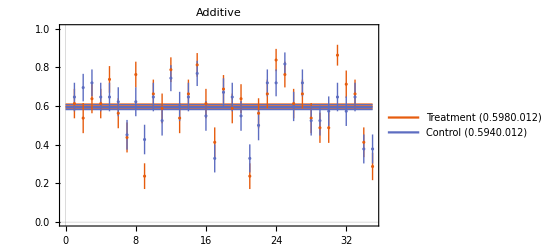

```mathematica
Show[errorbar,intervals]
```